# Lotka-Volterra model from ecology (competitive cohabitation)

## Jacobian and linearized systems’ matrices evaluated about the fixed points, and phase portrait

System

((3-x) x-2 x y
-x y+(2-y) y)

Jacobian matrix

(3-2 x-2 y | -2 x
-y | 2-x-2 y)

Jacobian matric about f.p.s

{(-1 | 0
-2 | -2),(-1 | -2
-1 | -1),(-3 | -6
0 | -1),(3 | 0
0 | 2)}

Determinants

{2,-1,3,6}

Trace

{-3,-2,-4,5}

Eigenvalues

{{-2,-1},{-1-√2,-1+√2},{-3,-1},{3,2}}

Eigenvektors

{{{0,1},{-1,2}},{{√2,1},{-√2,1}},{{1,0},{-3,1}},{{1,0},{0,1}}}

F.p.s coordinates

{{0,2},{1,1},{3,0},{0,0}}

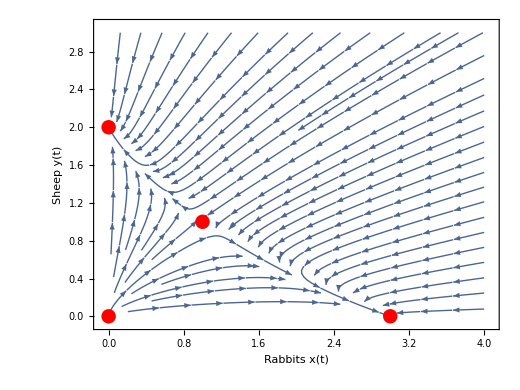
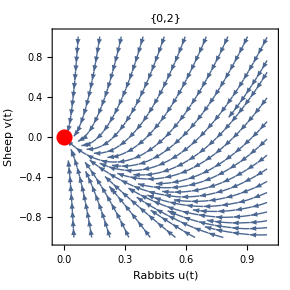
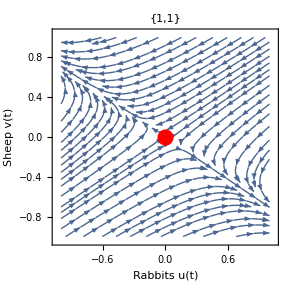
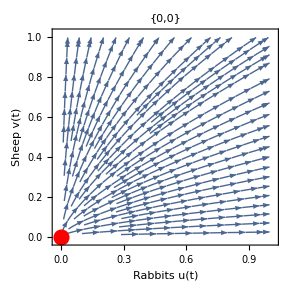
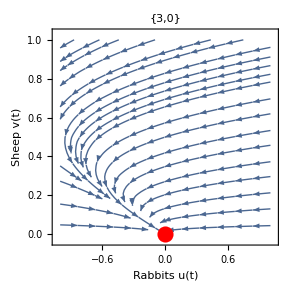
-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Clear[diffX,diffY,x,y];
diffX=x (3-x)-2 x y;
diffY=y (2-y)-x y;
fixedpoints=Solve[{diffX==0,diffY==0},{x,y}];
a={diffX,diffY};
Print[Style["System",18,Blue]]
MatrixForm[a]
Print[Style["Jacobian matrix",18,Blue]]
D[a,{{x,y}}]//MatrixForm (*Jacobian*)
Jfp=D[a,{{x,y}}]/.fixedpoints ; (*lin. systems' matrices about f.p.s*)
Print[Style["Jacobian matric about f.p.s",18,Blue]]
Map[MatrixForm][Jfp]
Print[Style["Determinants",18,Blue]]
Map[Det][Jfp]
Print[Style["Trace",18,Blue]]
Map[Tr][Jfp]
Print[Style["Eigenvalues",18,Blue]]
Map[Eigenvalues][Jfp]
Print[Style["Eigenvektors",18,Blue]]
Map[Eigenvectors][Jfp]
Print[Style["F.p.s coordinates",18,Blue]]
coordinates={x,y}/.fixedpoints

fixedp=Graphics[{PointSize[0.02],Red,Point[coordinates]}];
fixedp0=Graphics[{PointSize[0.04],Red,Point[{0,0}]}];
sp=Show[StreamPlot[{diffX,diffY},{x,0,4},{y,0,3},FrameLabel->{"Rabbits" x[t],"Sheep" y[t]},LabelStyle->18,ImageSize->520,AspectRatio->3/4],fixedp];
spFP1=Show[StreamPlot[ Jfp[[1]].({{x}, {y}}),{x,0,1},{y,-1,1},FrameLabel->{"Rabbits" u[t],"Sheep" v[t]},PlotLabel-> coordinates[[1]],LabelStyle->18,ImageSize->290],fixedp0];
spFP2=Show[StreamPlot[ Jfp[[2]].({{x}, {y}}),{x,-1,1},{y,-1,1},FrameLabel->{"Rabbits" u[t],"Sheep" v[t]},PlotLabel-> coordinates[[2]],LabelStyle->18,ImageSize->290],fixedp0];
spFP3=Show[StreamPlot[ Jfp[[3]].({{x}, {y}}),{x,-1,1},{y,0,1},FrameLabel->{"Rabbits" u[t],"Sheep" v[t]},PlotLabel-> coordinates[[3]],LabelStyle->18,ImageSize->290],fixedp0];
spFP4=Show[StreamPlot[ Jfp[[4]].({{x}, {y}}),{x,0,1},{y,0,1},FrameLabel->{"Rabbits" u[t],"Sheep" v[t]},PlotLabel-> coordinates[[4]],LabelStyle->18,ImageSize->290],fixedp0];
Grid[{{sp,SpanFromLeft},
{spFP1,spFP2},
{spFP4,spFP3}},Frame->All]
```

## Lotka-Volterra integrated solutions

```mathematica
Clear[diffX,diffY,x,y]
imagesize=350;maxT=15;

diffX=x (3-x)-2 x y;
diffY=y (2-y)-x y;
difX=x[t] (3-x[t])-2 x[t] y[t];
difY=y[t] (2-y[t])-x[t] y[t];
splot=StreamPlot[{diffX,diffY},{x,-1,4},{y,-1,3},FrameLabel->{x[t],y[t]},ImageSize->imagesize,LabelStyle->16];
fixedpoints=Solve[{diffX==0,diffY==0},{x,y}];
coordinates={x,y}/.fixedpoints;
fixedp=Graphics[{PointSize[0.03],Red,Point[coordinates]}];

Manipulate[
integration=NDSolve[{
x'[t]==difX,
y'[t]==difY,
x[0]==point[[1]],y[0]==point[[2]]},
{x,y},{t,0,T}];
trajectory=ParametricPlot[
Evaluate[{x[t],y[t]}/.integration],
{t,0,T},PlotStyle->Red];
solx=Plot[Evaluate[x[t]/.integration],
{t,0,T},PlotRange-> All,AxesLabel-> {t,x[t]},PlotLabel->"Rabbits",ImageSize->imagesize,LabelStyle->16];
soly=Plot[Evaluate[y[t]/.integration],
{t,0,T},PlotRange-> All,AxesLabel-> {t,y[t]},PlotLabel->"Sheep",ImageSize->imagesize,LabelStyle->16];
region=RegionPlot[0<x<4&&0<y<3,{x,-2,4},{y,-1,3},PlotStyle->Opacity[0.25],BoundaryStyle->None];
Grid[{{Show[splot,region,trajectory,fixedp],soly},{solx}},Frame->All],
{{T,0.4 maxT,"Integration time, t"},1,maxT,Appearance->"Labeled"},{{point,{0.1,0.1}},Locator}, SaveDefinitions->True,TrackedSymbols:>{T,point}]
```

Creation of this notebook was supported by IT Academy program of Information Technology Foundation for Education (HITSA).